```mathematica
σ0=SparseArray[{{1,1}->1,{2,2}->1},2];
σx=SparseArray[{{1,2}->1,{2,1}->1},2];
σy=SparseArray[{{1,2}->-ⅈ,{2,1}->ⅈ},2];
σz=SparseArray[{{1,1}->1,{2,2}->-1},2];
σkx[k_,n_]:=Block[{t},If[k==1,t=σx,{t=σ0;t=Nest[KroneckerProduct[σ0,#]&,t,k-2];t=KroneckerProduct[σx,t];}];
t=Nest[KroneckerProduct[σ0,#]&,t,n-k];
Return[t]];
σky[k_,n_]:=Block[{t},If[k==1,t=σy,{t=σ0;t=Nest[KroneckerProduct[σ0,#]&,t,k-2];t=KroneckerProduct[σy,t];}];
t=Nest[KroneckerProduct[σ0,#]&,t,n-k];
Return[t]];
σkz[k_,n_]:=Block[{t},If[k==1,t=σz,{t=σ0;t=Nest[KroneckerProduct[σ0,#]&,t,k-2];t=KroneckerProduct[σz,t];}];
t=Nest[KroneckerProduct[σ0,#]&,t,n-k];
Return[t]];
σkI[n_]:=Block[{t},
t=σ0;
t=Nest[KroneckerProduct[σ0,#]&,t,n-1];
Return[t]];
commutator[A_,B_]:=A.B-B.A;
groundSystem[X_]:=Map[{#⟦1⟧}&,Transpose[SortBy[Transpose[Eigensystem[Normal[X]]],First]]];
groundSystem[X_,n_]:=Map[#⟦1;;n⟧&,Transpose[SortBy[Transpose[Eigensystem[Normal[X]]],First]]];
HmixedIsing[J_,hx_,hz_,n_]:=J*Sum[σkz[i,n].σkz[Mod[i+1,n,1],n],{i,n}]+hx*Sum[σkx[i,n],{i,n}]+hz*Sum[σkz[i,n],{i,n}];
HmixedIsingNoP[J_,hx_,hz_,n_]:=J*Sum[σkz[i,n].σkz[Mod[i+1,n,1],n],{i,n-1}]+hx*Sum[σkx[i,n],{i,n}]+hz*Sum[σkz[i,n],{i,n}];
randomHmixedIsing[J_,hx_,hz_,n_]:=J*Sum[RandomReal[{-1,1}]*σkz[i,n].σkz[Mod[i+1,n,1],n],{i,n}]+hx*Sum[RandomReal[{-1,1}]*σkx[i,n],{i,n}]+hz*Sum[RandomReal[{-1,1}]*σkz[i,n],{i,n}];
```

{-3.,-3.}

{0.,-2.77556×10^-17,-0.00917694,-0.0364517,-0.0897918,-0.174612,-0.291314,-0.433108,-0.586321,-0.734591,-0.864977}

{0.125,0.125,0.126149,0.129585,0.136403,0.147517,0.163375,0.183588,0.206724,0.230617,0.25316}

{0,0.,-0.479616,-0.956227,-1.42198,-1.85918,-2.23763,-2.51748,-2.66116,-2.65183,-2.50709}

{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0}

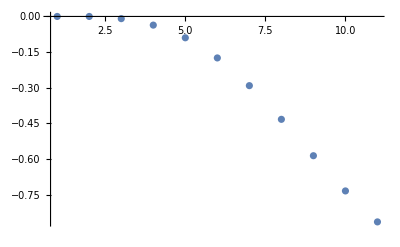

```mathematica
nq=4;
J=1.0;
hx=0.0;
hz=0.0;
hp=-HmixedIsingNoP[J,hx,hz,nq];
hd=Sum[σkx[i,nq],{i,nq}];
hcd=0*Sum[σky[i,nq],{i,nq}];
ψ0=Normalize[Table[1,{i,2^nq}]];
gs=groundSystem[hp,2];
gs[[1]]
ψgs=gs[[2]][[1;;2]];
ψt=ψ0;
Δt0=0.02;
Bk=0;
Ck=0;
Dk=0;
eList={Re[Conjugate[ψ0].hp.ψ0]};
fidList={Sum[Abs[Conjugate[ψ0].ψgs[[i]]]^2,{i,Length[ψgs]}]};
Bks={Bk};
CKs={Ck};
DKs={Dk};
Do[
Δt=Δt0;
hpt=hp+0*Exp[-(k-1)*0.2]*Sum[σkz[i,nq],{i,nq}];
Bk=Re[-ⅈ*Conjugate[ψt].commutator[hd,hpt].ψt];
Ck=Re[-ⅈ*Conjugate[ψt].commutator[hcd,hpt].ψt];
ψt=MatrixExp[-ⅈ hpt* Δt,ψt];
ψt=MatrixExp[-ⅈ hd* Δt*Bk,ψt];
ψt=MatrixExp[-ⅈ hcd* Δt*Ck,ψt];
AppendTo[Bks,Bk];
AppendTo[CKs,Ck];
AppendTo[eList,Re[Conjugate[ψt].hp.ψt]];
AppendTo[fidList,Sum[Abs[Conjugate[ψt].ψgs[[i]]]^2,{i,Length[ψgs]}]]
,{k,1,10}]
eList
fidList
Bks
CKs
DKs
ListPlot[eList,PlotRange->All]
```

{-3.,-3.}

{0.,-0.293202,-1.27397,-2.39834,-2.87258,-2.96008,-2.9724,-2.97415,-2.97439,-2.97442,-2.97443}

{0.125,0.199768,0.465697,0.803401,0.95661,0.985574,0.989665,0.990239,0.990315,0.990319,0.990315}

{0,0.,-0.867184,-1.72631,-1.80339,-1.07022,-0.488653,-0.213194,-0.0923301,-0.0386815,-0.0141094}

{0,8.,9.76316,9.84056,6.43554,2.65909,0.933731,0.327049,0.113395,0.0353745,0.00621081}

{0}

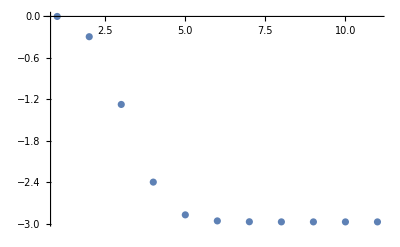

```mathematica
nq=4;
J=1.0;
hx=0.0;
hz=0.0;
hp=-HmixedIsingNoP[J,hx,hz,nq];
hd=Sum[σkx[i,nq],{i,nq}];
hcd=Sum[σky[i,nq],{i,nq}];
ψ0=Normalize[Table[1,{i,2^nq}]];
gs=groundSystem[hp,2];
gs[[1]]
ψgs=gs[[2]][[1;;2]];
ψt=ψ0;
Δt0=0.02;
Bk=0;
Ck=0;
Dk=0;
eList={Re[Conjugate[ψ0].hp.ψ0]};
fidList={Sum[Abs[Conjugate[ψ0].ψgs[[i]]]^2,{i,Length[ψgs]}]};
Bks={Bk};
CKs={Ck};
DKs={Dk};
Do[
Δt=Δt0;
hpt=hp+1*Exp[-(k-1)*0.2]*Sum[σkz[i,nq],{i,nq}];
Bk=Re[-ⅈ*Conjugate[ψt].commutator[hd,hpt].ψt];
Ck=Re[-ⅈ*Conjugate[ψt].commutator[hcd,hpt].ψt];
ψt=MatrixExp[-ⅈ hpt* Δt,ψt];
ψt=MatrixExp[-ⅈ hd* Δt*Bk,ψt];
ψt=MatrixExp[-ⅈ hcd* Δt*Ck,ψt];
AppendTo[Bks,Bk];
AppendTo[CKs,Ck];
AppendTo[eList,Re[Conjugate[ψt].hp.ψt]];
AppendTo[fidList,Sum[Abs[Conjugate[ψt].ψgs[[i]]]^2,{i,Length[ψgs]}]]
,{k,1,10}]
eList
fidList
Bks
CKs
DKs
ListPlot[eList,PlotRange->All]
```